```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
SetDirectory["/users/home/arway/Desktop/Work/Data/Acenet/MAG/2june16"]
```

/users/home/arway/Desktop/Work/Data/Acenet/MAG/2june16

```mathematica
DATA=Import["SF1_96.dat","Table"];
```

```mathematica
DATA[[1]]
```

{-3.14159,0.,0.0083}

```mathematica
ListPlot3D[DATA]
```

-Graphics3D-

```mathematica
??AxesLabel
```

AxesLabel is an option for graphics functions that specifies labels for axes.

Attributes[AxesLabel]={Protected}

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[Sqrt[(4-Sqrt[16-6 (1-Cos[4 ϕ])])/(1-Cos[4 ϕ])]]]
```

```mathematica
SFcontour=ListContourPlot[DATA,InterpolationOrder->50,PlotLegends->Automatic,AxesLabel->{"Phi","Theta"}]
```

-Graphics-

```mathematica
pheta=Import["GenAng.dat","Table"];
```

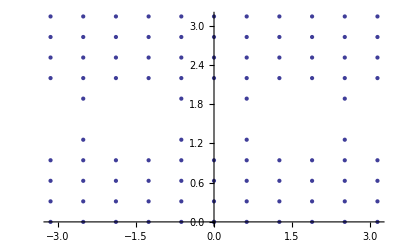

```mathematica
phetapair=ListPlot[pheta]
```

```mathematica
Show[SFcontour,Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{-π,π},{0,2 π}}],phetapair]
```

-Graphics-

```mathematica
ListPointPlot3D[DATA]
```

-Graphics3D-

```mathematica
SphericaPlot3D[DATA]
```

SphericalPlot3D::argr: SphericalPlot3D called with 1 argument; 3 arguments are expected.

SphericalPlot3D[DATA]

```mathematica
DATA[[All,1]]
```

{-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-2.51327,-1.88496,-1.88496,-1.88496,-1.88496,-1.88496,-1.88496,-1.88496,-1.88496,-1.25664,-1.25664,-1.25664,-1.25664,-1.25664,-1.25664,-1.25664,-1.25664,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,-0.628319,0.,0.,0.,0.,0.,0.,0.,0.,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,0.628319,1.25664,1.25664,1.25664,1.25664,1.25664,1.25664,1.25664,1.25664,1.88496,1.88496,1.88496,1.88496,1.88496,1.88496,1.88496,1.88496,2.51327,2.51327,2.51327,2.51327,2.51327,2.51327,2.51327,2.51327,2.51327,2.51327,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159}

```mathematica
data=Flatten[Table[{{DATA[[i,1]],DATA[[i,2]]},DATA[[i,3]]},{i,1,Length[DATA]}],1];
```

```mathematica
f=Interpolation[data];
```

```mathematica
f
```

InterpolatingFunction[{{1.,192.}},<>]

```mathematica
f[1,0]
```

InterpolatingFunction[{{1.,192.}},<>][1,0]

```mathematica
SphericalPlot3D[f[phi,theta],{theta,0,Pi},{phi,-π,π}]
```

-Graphics3D-